```mathematica
f[x_]=exp(x-(x/4)^2)*th((x/11)^3+1/3);
```

```mathematica
a=0;
b=6;
n=6;
```

```mathematica
Chebush=Table[Cos[Pi*(2*i+1)/(2*n+2)],{i,0,n}];
```

```mathematica
T1=Table[{(a+b)/2+(b-a)/2*Chebush[[n-i+1]],f[(a+b)/2+(b-a)/2*Chebush[[n-i+1]]]},{i,0,n}]//N;
```

```mathematica
TableForm[T1]
```

0.0752163 | 0.700699
0.654506 | 5.22344
1.69835 | 6.83037
3. | 3.90999
4.30165 | 2.21924
5.34549 | 2.49984
5.92478 | 2.96864

```mathematica
Array[dif,{n+1},{n+1},{0,0}];
For[k=1,k≤ n,k++,
For[i=n,i≥ n-k,i--,
dif[i,k]=""
]
];
For[i=0,i≤n,i++,
dif[i,0]=T1[[i+1,2]]
];
For[k=1,k≤n,k++,
For[i=0,i≤n-k,i++,
dif[i,k]=(dif[i+1,k-1]-dif[i,k-1])/(T1[[i+k+1,1]]-T1[[i+1,1]])
]
];
T2=Array[dif,{n+1,n+1},{0,0}];
PaddedForm[TableForm[T2],{5,2}]
```

0.70 |    7.81 |   -3.86 |    0.77 |   -0.05 |   -0.01 |    0.00
   5.22 |    1.54 |   -1.61 |    0.54 |   -0.10 |    0.01 | 
   6.83 |   -2.24 |    0.36 |    0.08 |   -0.05 |  | 
   3.91 |   -1.30 |    0.67 |   -0.11 |  |  | 
   2.22 |    0.27 |    0.33 |  |  |  | 
   2.50 |    0.81 |  |  |  |  | 
   2.97 |  |  |  |  |  |

```mathematica
Pnr[x_]=dif[0,0];
g[x_]=1;
For[k=1,k≤n,k++,
g[x_]=g[x]*(x-table[[k,1]]);
Pnr[x_]=Pnr[x]+dif[0,k]*g[x];
]
Pnr[x_]=Simplify[Pnr[x]]
```

0.42553+9.15346 x-4.67557 x^2+0.766461 x^3+0.047333 x^4-0.0315357 x^5+0.00306701 x^6

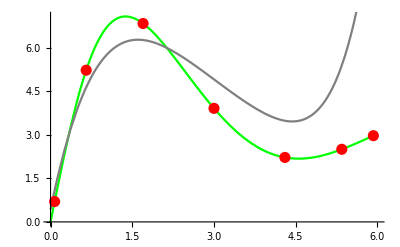

```mathematica
gr1:=Plot[f[x],{x,0,6},PlotStyle->Green];
gr2:=Plot[Pnr[x],{x,0,6},PlotStyle->Gray];
Show[gr1,gr2,ListPlot[T1,PlotStyle->{ Red,PointSize[0.02]}]]
```

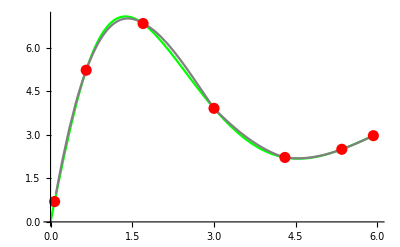

```mathematica
IntF=Interpolation[T1];
gr1:=Plot[f[x],{x,0,6},PlotStyle->Green];
gr2:=Plot[IntF[x],{x,0.1,6},PlotStyle->Gray];
Show[gr1,gr2,ListPlot[T1,PlotStyle->{ Red,PointSize[0.02]}]]
```

```mathematica
f[2.4316]
```

5.26999

```mathematica
Pnr[2.4316]
```

5.66548

```mathematica
IntF[2.4316]
```

5.45624

```mathematica
R[x_]=Abs[f[x]-Pnr[x]];
```

```mathematica
FindMaximum[R[x],{x,0.1,6}]
```

{0.427284,{x→-0.0190324}}

```mathematica
R[x_]=Abs[f[x]-IntF[x]];
```

```mathematica
FindMaximum[R[x],{x,0.1,6}]
```

{0.143,{x→0.295148}}

```mathematica
a=0;
b=6;
n=10;
```

```mathematica
Chebush=Table[Cos[Pi*(2*i+1)/(2*n+2)],{i,0,n}];
```

```mathematica
T1=Table[{(a+b)/2+(b-a)/2*Chebush[[n-i+1]],f[(a+b)/2+(b-a)/2*Chebush[[n-i+1]]]},{i,0,n}]//N;
```

```mathematica
TableForm[T1]
```

0.0305357 | 0.284984
0.271104 | 2.46079
0.732751 | 5.6344
1.37808 | 7.07322
2.1548 | 5.94274
3. | 3.90999
3.8452 | 2.52522
4.62192 | 2.18105
5.26725 | 2.4456
5.7289 | 2.80258
5.96946 | 3.00653

```mathematica
Array[dif,{n+1},{n+1},{0,0}];
For[k=1,k≤ n,k++,
For[i=n,i≥ n-k,i--,
dif[i,k]=""
]
];
For[i=0,i≤n,i++,
dif[i,0]=T1[[i+1,2]]
];
For[k=1,k≤n,k++,
For[i=0,i≤n-k,i++,
dif[i,k]=(dif[i+1,k-1]-dif[i,k-1])/(T1[[i+k+1,1]]-T1[[i+1,1]])
]
];
T2=Array[dif,{n+1,n+1},{0,0}];
PaddedForm[TableForm[T2],{5,2}]
```

0.28 |    9.04 |   -3.09 |   -0.82 |    0.79 |   -0.26 |    0.06 |   -0.01 |    0.00 |   -0.00 |    4.72×10^-6
   2.46 |    6.87 |   -4.20 |    0.85 |    0.01 |   -0.05 |    0.01 |   -0.00 |    0.00 |   -0.00 | 
   5.63 |    2.23 |   -2.59 |    0.88 |   -0.15 |    0.01 |   -0.00 |    0.00 |    0.00 |  | 
   7.07 |   -1.46 |   -0.59 |    0.42 |   -0.09 |    0.01 |   -0.00 |    0.00 |  |  | 
   5.94 |   -2.41 |    0.45 |    0.11 |   -0.06 |    0.01 |   -0.00 |  |  |  | 
   3.91 |   -1.64 |    0.74 |   -0.06 |   -0.03 |    0.01 |  |  |  |  | 
   2.53 |   -0.44 |    0.60 |   -0.14 |   -0.01 |  |  |  |  |  | 
   2.18 |    0.41 |    0.33 |   -0.16 |  |  |  |  |  |  | 
   2.45 |    0.77 |    0.11 |  |  |  |  |  |  |  | 
   2.80 |    0.85 |  |  |  |  |  |  |  |  | 
   3.01 |  |  |  |  |  |  |  |  |  |

```mathematica
Pnr[x_]=dif[0,0];
g[x_]=1;
For[k=1,k≤n,k++,
g[x_]=g[x]*(x-table[[k,1]]);
Pnr[x_]=Pnr[x]+dif[0,k]*g[x];
]
Pnr[x_]=Simplify[Pnr[x]]
```

0.00643725+9.07652 x+1.73009 x^2-8.02667 x^3+5.39057 x^4-1.93183 x^5+0.430981 x^6-0.0610887 x^7+0.00528309 x^8-0.000249053 x^9+4.71686×10^-6 x^10

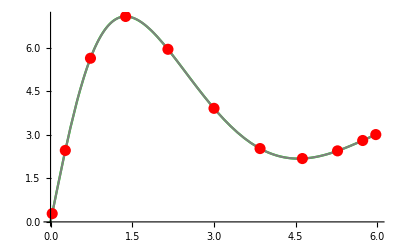

```mathematica
gr1:=Plot[f[x],{x,0,6},PlotStyle->Green];
gr2:=Plot[Pnr[x],{x,0,6},PlotStyle->Gray];
Show[gr1,gr2,ListPlot[T1,PlotStyle->{ Red,PointSize[0.02]}]]
```

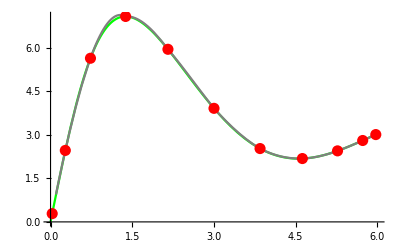

```mathematica
IntF=Interpolation[T1];
gr1:=Plot[f[x],{x,0,6},PlotStyle->Green];
gr2:=Plot[IntF[x],{x,0.1,6},PlotStyle->Gray];
Show[gr1,gr2,ListPlot[T1,PlotStyle->{ Red,PointSize[0.02]}]]
```

```mathematica
f[2.4316]
```

5.26999

```mathematica
Pnr[2.4316]
```

5.2685

```mathematica
IntF[2.4316]
```

5.29934

```mathematica
R[x_]=Abs[f[x]-Pnr[x]];
```

```mathematica
FindMaximum[R[x],{x,0.15,6}]
```

{0.00639676,{x→0.120949}}

```mathematica
R[x_]=Abs[f[x]-IntF[x]];
```

```mathematica
FindMaximum[R[x],{x,0.15,6}]
```

{0.0152185,{x→0.134017}}